# Model C6: Geometric Circle Area Proof

Here we present a proof of the area of a circle, together with a visualization. The plan of the proof is to find the area of the general regular n-gon that is inscribed in the circle and circumscribed, and then take their the limits of those areas as n goes to infinity, and finally to utilize the Squeeze Theorem to show that the unit circle, trapped between them, has area π r^2.

We start with the area of the inscribed polygon.

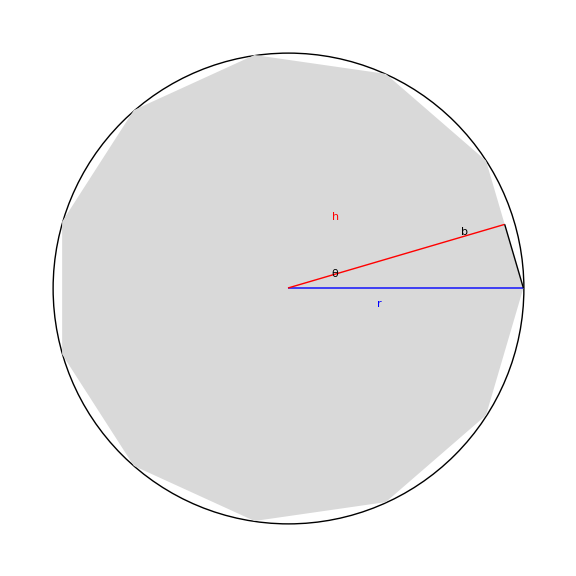

```mathematica
Module[{n,θ,r,h,shif,ϕ},n=11;θ=(π(n-2))/n;r=1;h=r Sin[θ/2];shif=0;ϕ=π/2-θ;
Graphics[{Black,Circle[{0,0},1],LightGray,Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2π,2π/n}]],Blue,Line[{{0,0},{1,0}}],Style[Text["r",{.39,-.07}],{Blue,FontSize->45}],Red,Line[{{0,0},h{Cos[(2π)/(2n)],Sin[(2π)/(2n)]}}],Style[Text["h",{.2,.3}],{Red,FontSize->45}],Black,Line[{{1,0},h{Cos[(2π)/(2n)],Sin[(2π)/(2n)]}}],Style[Text["θ",{.2,.06}],{Black,FontSize->30}],Style[Text["b",{.75,.24}],{Black,FontSize->45}]},ImageSize->Large]]
```

The area of a regular n-gon can be computer as the area of the above triangle times 2n. θ is 2π divided by the number of sides and divided by 2, so π/n. It’s a right triangle, with hypotenuse r, the radius, height h, and side length, b, is half of the side length of the polygon. Cosθ = h/r → h = rCosθ, and similarly b = rSinθ. So, then, the area of this triangle is 1/2rSinθ rCosθ, and the area of the inscribed regular n-gon is 2n times that, so n r^2 Sinθ Cosθ. We’ll use this later, now we do the circumscribed regular n-gon:

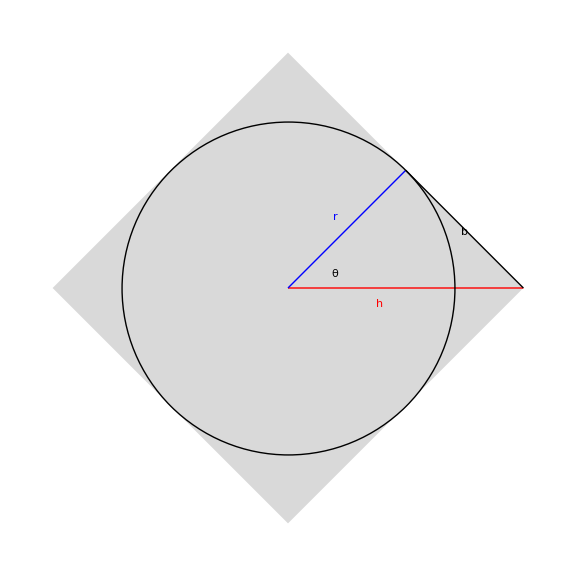

```mathematica
Module[{n,θ,r,h,shif,ϕ},
n=4;θ=(π(n-2))/n;r=1;h=r Sin[θ/2];shif=0;ϕ=π/2-θ;
Graphics[{LightGray,Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2π,2π/n}]],Red,Line[{{0,0},{1,0}}],Style[Text["h",{.39,-.07}],{Red,FontSize->45}],Blue,Line[{{0,0},h{Cos[(2π)/(2n)],Sin[(2π)/(2n)]}}],Style[Text["r",{.2,.3}],{FontSize->45}],Black,Line[{{1,0},h{Cos[(2π)/(2n)],Sin[(2π)/(2n)]}}],Style[Text["θ",{.2,.06}],{Black,FontSize->30}],Style[Text["b",{.75,.24}],{Black,FontSize->45}],Black,Circle[{0,0},h]},ImageSize->Large]]
```

Here our triangle that we will use looks quite similar, except this time the hypotenuse is our h side, and the radius of the circle is one of the legs. The length of the radius leg, is, of course, r, and the length of the other leg, b, is r Tanθ. We note that h = r/Cosθ, that is, for below when we need to draw the regular n-gon circumscribed around the circle with radius r, we can instead think of it as the regular n-gon inscribed in the circle of radius h = r/Cosθ. So, the area of the triangle is 1/2b r = 1/2 r^2 Tanθ = (r^2 Tanθ)/2, and the area of the circumscribed regular n-gon is 2n times that, n r^2 Tanθ.

Now, let’s put this together - following is a model where you can specify the number of sides of the polygon, and printed will be the area of the inscribed polygon and that of the circumscribed polygon.

```mathematica
Module[{max,r},max=5000;r=1;
Manipulate[Graphics[{White,EdgeForm[Directive[{Thick,Red}]],Polygon[Table[r/Cos[π/n]{Cos[θ],Sin[θ]},{θ,0,2π,2π/n}]],EdgeForm[Directive[{Thick,Blue}]],Polygon[Table[r{Cos[θ],Sin[θ]},{θ,0,2π,2π/n}]],Blue,Style[Text["Inscribed n-gon Area = "<>ToString[n r^2 Sin[π/n]Cos[π/n]//N[#,10]&],{0,1.4}],{FontSize->20}],Red,Style[Text["Circumscribed n-gon Area = "<>ToString[n r^2 Tan[π/n]//N[#,10]&],{0,1.25}],{FontSize->20}],Black,Thick,Circle[{0,0},1]},ImageSize->Large,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{{n,4},3,max,1}]]
```

Visually, everything is going how we wanted. We are convinced that the Squeeze Theorem is appropriate, as the area of the circumscribed polygon is certainly strictly greater than that of the circle, and the area of inscribed polygon is strictly less than that of the circle. As our final step, we take the limits of these areas as n goes to infinity to show they meet up in the middle at π r^2.

Area of the inscribed regular n-gon:

```mathematica
Block[{r,n},Limit[n r^2 Sin[π/n]Cos[π/n],n->∞]]
```

π r^2

Area of the circumscribed regular n-gon:

```mathematica
Block[{r,n},Limit[n r^2 Tan[π/n],n->∞]]
```

π r^2

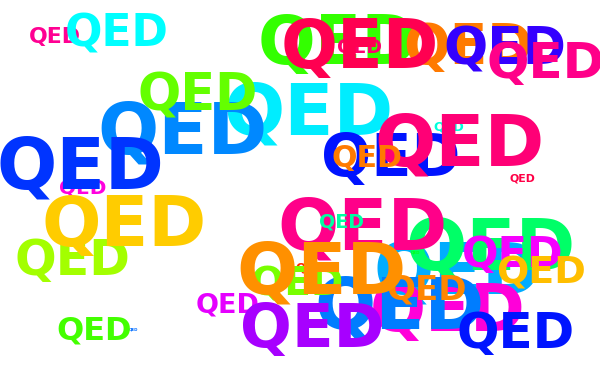

```mathematica
Graphics[Table[Text[Style["QED",Hue[RandomReal[]],Italic,Bold,RandomInteger[80]],RandomReal[.3,{2}],Automatic,RandomReal[{-1,1},{2}]],{40}],AspectRatio->1/GoldenRatio,ImageSize->600]
```